```mathematica
xbar=(ρ-σ-δ1*σ)/(ρ-σ)
ybar=(μ((ρ-σ-δ1*σ))^2)/(μ(ρ-σ-δ1*σ)^2+(ρ-σ)(η*ρ+δ2*σ))
zbar=(γ*ρ-γ*σ-δ3*σ)/(γ(ρ-σ))
wbar=(ρ-σ)/ρ
```

(ρ-σ-δ1 σ)/(ρ-σ)

(μ (ρ-σ-δ1 σ)^2)/(μ (ρ-σ-δ1 σ)^2+(ρ-σ) (η ρ+δ2 σ))

(γ ρ-γ σ-δ3 σ)/(γ (ρ-σ))

(ρ-σ)/ρ

```mathematica
S[f_,v_]:=D[f,v]*(v/f)
```

```mathematica
S[{xbar,ybar,zbar,wbar},σ]
```

{((ρ-σ) σ ((-1-δ1)/(ρ-σ)+(ρ-σ-δ1 σ)/(ρ-σ)^2))/(ρ-σ-δ1 σ),1/(μ (ρ-σ-δ1 σ)^2)σ (μ (ρ-σ-δ1 σ)^2+(ρ-σ) (η ρ+δ2 σ)) (-(μ (ρ-σ-δ1 σ)^2 (-η ρ+δ2 (ρ-σ)-δ2 σ+2 (-1-δ1) μ (ρ-σ-δ1 σ)))/((μ (ρ-σ-δ1 σ)^2+(ρ-σ) (η ρ+δ2 σ))^2)+(2 (-1-δ1) μ (ρ-σ-δ1 σ))/(μ (ρ-σ-δ1 σ)^2+(ρ-σ) (η ρ+δ2 σ))),(γ (ρ-σ) σ ((-γ-δ3)/(γ (ρ-σ))+(γ ρ-γ σ-δ3 σ)/(γ (ρ-σ)^2)))/(γ ρ-γ σ-δ3 σ),-σ/(ρ-σ)}

```mathematica
replacement={ρ->0.40,γ->0.75,δ3->0.20,δ1->0.55,μ->0.50,η->0.25,δ2->0.65}
```

{ρ→0.4,γ→0.75,δ3→0.2,δ1→0.55,μ→0.5,η→0.25,δ2→0.65}

```mathematica
values={xbar,ybar,zbar,wbar}/.replacement
```

{(0.4-1.55 σ)/(0.4-σ),(0.5 (0.4-1.55 σ)^2)/(0.5 (0.4-1.55 σ)^2+(0.4-σ) (0.1+0.65 σ)),(1.33333 (0.3-0.95 σ))/(0.4-σ),2.5 (0.4-σ)}

```mathematica
valuesplot=Plot[values,{σ,0.2,0.35},PlotLegends->Placed[{Style["xbar",36],Style["ybar",36],Style["zbar",36],Style["wbar",36]},{Bottom,Bottom}],AxesStyle->Thick,TicksStyle->32,PlotStyle->Directive[Thickness[0.005]]]
```

-Graphics-

```mathematica
Show[valuesplot,RegionPlot[0.4/1.55≤x≤0.4/(1+0.2/0.75),{x,0,0.35},{y,-1.1,0.8},PlotStyle->{Opacity[0.10],Gray}],ImageSize->Full]
```

-Graphics-

```mathematica
sensitivities=S[values,σ]
```

{(((0.4-1.55 σ)/(0.4-σ)^2-1.55/(0.4-σ)) (0.4-σ) σ)/(0.4-1.55 σ),1/(0.4-1.55 σ)^2 2. (-(1.55 (0.4-1.55 σ))/(0.5 (0.4-1.55 σ)^2+(0.4-σ) (0.1+0.65 σ))-(0.5 (0.4-1.55 σ)^2 (-0.1-1.55 (0.4-1.55 σ)+0.65 (0.4-σ)-0.65 σ))/((0.5 (0.4-1.55 σ)^2+(0.4-σ) (0.1+0.65 σ))^2)) (0.5 (0.4-1.55 σ)^2+(0.4-σ) (0.1+0.65 σ)) σ,(0.75 (-1.26667/(0.4-σ)+(1.33333 (0.3-0.95 σ))/(0.4-σ)^2) (0.4-σ) σ)/(0.3-0.95 σ),-(1. σ)/(0.4-σ)}

```mathematica
sens=Plot[sensitivities,{σ,0,0.4},PlotLegends->Placed[{Style["S(x̄,σ)",36],Style["S(ȳ,σ)",36],Style["S(z̄,σ)",36],Style["S(w̄,σ)",36]},{Bottom,Bottom}],ImageSize->Full,PlotStyle->Directive[Thickness[0.005],AxesStyle->Thick],TicksStyle->32]
```

-Graphics-

```mathematica
Show[sens,RegionPlot[0.4/1.55≤x≤0.4/(1+0.2/0.75),{x,0,0.35},{y,-23,29},PlotStyle->{Opacity[0.10],Gray}],ImageSize->Full]
```

-Graphics-

```mathematica
0.4/1.55
```

0.258065

```mathematica
0.4/(1+(0.2/0.75))
```

0.315789

```mathematica
constraints={δ1>(ρ-σ)/σ,δ3<γ(ρ-σ)/σ}/.replacement
```

{0.55>(0.4-σ)/σ,0.2<(0.75 (0.4-σ))/σ}

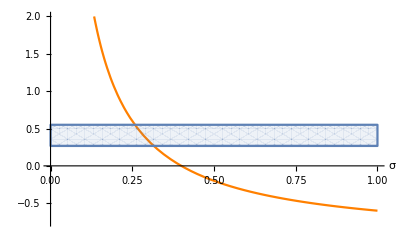

```mathematica
Show[Plot[(0.4-σ)/σ,{σ,0,1},PlotRange->{-0.75,2},AxesLabel->{"σ",None},PlotStyle->Orange],RegionPlot[0.2/0.75<y<0.55,{σ,0,1},{y,-0.6,2},PlotStyle->Opacity[0.1]]]
```

```mathematica
zbar/.replacement
```

(1.33333 (0.3-0.95 σ))/(0.4-σ)

```mathematica
zbar1d=D[zbar/.replacement,{σ,1}]
```

-1.26667/(0.4-σ)+(1.33333 (0.3-0.95 σ))/(0.4-σ)^2

```mathematica
(zbar/.replacement)/.{σ->0.26}
```

0.504762

```mathematica
(zbar/.replacement)/.{σ->0.31}
```

0.0814815

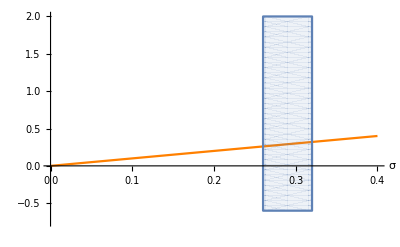

```mathematica
Show[Plot[σ,{σ,0,0.4},PlotRange->{-0.75,2},AxesLabel->{"σ",None},PlotStyle->Orange],RegionPlot[0.26<σ<0.32,{σ,0,1},{y,-0.6,2},PlotStyle->Opacity[0.1]]]
```

```mathematica
bounds=0.26≤σ≤0.32
```

0.26≤σ≤0.32

```mathematica
Maximize[{wbar/.replacement,bounds},σ]
```

{0.35,{σ→0.26}}

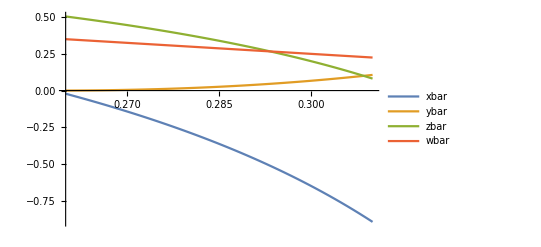

```mathematica
Plot[values,{σ,0.26,0.31},PlotLegends->{"xbar","ybar","zbar","wbar"}]
```

```mathematica
S[0.26s/d,s]
```

1.

```mathematica
S[0.26s/d,d]
```

-1.

```mathematica
Plot3D[0.26k/s,{k,0,1},{s,0,1},AxesLabel->{Style["k",36],Style["s",36],Style["D",36]},PlotRange->Automatic,ImageSize->Full,ColorFunction->"Rainbow",AxesStyle->Thick]
```

-Graphics3D-